```mathematica
ClearAll["Global`*"];
```

```mathematica
dat=ReadList["KBHSH1.dat",{Number,Number,Number,Number,Number,Number,Number}];
nx=251;ny=30;
xmax=dat[[251,1]];xmin=dat[[1,1]];
ymax=dat[[nx*ny,2]];ymin=dat[[1,2]];
rh=0.2;OmegaH=0.975;
```

```mathematica
cts =NSolve[OmegaH==Sqrt[x(x-rh)]/((rh-x)(rh-2x)),x];
ct=cts[[2,1,2]];
```

```mathematica
M=(rh-2ct)/2.0
a = Sqrt[ct(ct-rh)](rh-2ct)/2/M
a/M
RH = M+Sqrt[M^2-a^2];
```

0.396219

0.383392

0.967627

```mathematica
Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2],1000]
```

```mathematica
f1=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,3]]]},{i,1,ny},{j,1,nx}];
f2=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,4]]]},{i,1,ny},{j,1,nx}];
f0=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],Exp[2*dat[[j+(i-1)*nx,5]]]},{i,1,ny},{j,1,nx}];
W=Table[{Xtor[dat[[j+(i-1)*nx,1]]],dat[[j+(i-1)*nx,2]],dat[[j+(i-1)*nx,7]]},{i,1,ny},{j,1,nx}];
H[r_]:=1-rh/r;
```

```mathematica
(*f1[[ny,All,2]] = N[π/2,5] ;(* mathematica being silly... *)
f1[[ny,All,2]]*)
```

```mathematica
if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
```

```mathematica
f1 = if1;
f2=if2;
f0=if0;
W=iW;
```

```mathematica
coords = {t,r,θ,ϕ};
n=Length[coords];
tt=-f0[r,θ]* H[r]+ f2[r,θ]*r^2*Sin[θ]^2W[r,θ]^2;
rr=f1[r,θ]/H[r] ;
θθ=f1[r,θ]*r^2;
ϕϕ=f2[r,θ]* r^2*Sin[θ]^2;
tϕ=+f2[r,θ]*r^2*Sin[θ]^2W[r,θ];

metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
metric//MatrixForm;
inversemetric=Simplify[Inverse[metric]];
inversemetric //MatrixForm;
Rtor[R_] := R - a^2/RH;
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*(D[metric[[s,j]],coords[[k]]]+D[metric[[s,k]],coords[[j]]]-D[metric[[j,k]],coords[[s]]]),{s,1,n}],{i,1,n},{j,1,n},{k,1,n}]]
geodesic:=geodesic=Simplify[Table[-Sum[christoffel[[i,j,k]] coords[[j]]' coords[[k]]',{j,1,n},{k,1,n}],{i,1,n}]]
```

```mathematica
(* the solver function. It takes in the max τ, the initial velocities in r,θ,ϕ and the initial coordinates in t,r,θ,ϕ. 
it calculates whether the trajectory is timelike or null from the variable χ and uinvar which is determined before 
calling the function *)
computeSoln[maxτi_,ivsi_,icsi_]:=Block[{ivs,ics,i,χ,tmp,soln},
ics=icsi;
ivs=Join[{χ},ivsi];
tmp=metric;
tmp=tmp/.Table[coords[[i]]->ics[[i]],{i,0,n}];
tmp=ivs.(tmp.ivs);
τend = maxτi;
χslv=Solve[tmp==uinvar,χ];
ivs[[1]]=Last[χ/.χslv];
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,coords,
{τ,0,maxτi},
Method->{"EventLocator","Event":>(Re[r[τ]]≤1.5*rh),"EventAction":>Throw[τend=τ,"StopIntegration"]}
];
soln]
(* this next function translates from spherical coordinates to Cartesian coordinates to make plotting simpler 
I want to plot in the R, i.e. BL, radial coordinates, so for solution 1, I have to translate to R via r = R - a^2/RH *)
sphslnToCartsln[soln_]:=Block[{xs,ys,zs},xs=(r[τ]+a^2/RH) Sin[θ[τ]] Cos[ϕ[τ]]/.soln ;ys=(r[τ]+a^2/RH) Sin[θ[τ]] Sin[ϕ[τ]]/.soln;zs=(r[τ]+a^2/RH) Cos[θ[τ]]/.soln;{xs,ys,zs}]
coordlist[τin_,soln_]:=Table[ToString[coords[[i]]]<>" = "<>{ToString[coords[[i]][τin]/.soln//First]},{i,1,n}]
```

```mathematica
genXYPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[2]]}//Flatten],{τ,0,τend},AxesLabel->{x,y},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[1]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{x,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot[Evaluate[{xyz[[2]],xyz[[3]]}//Flatten],{τ,0,τend},AxesLabel->{y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
genXYZPlot[mτ_,icsin_,ivsin_,hue_]:=Block[{xyz},
soln = computeSoln[mτ,ivsin,icsin];
xyz=sphslnToCartsln[soln];
If[mτ==τend,Print["The particle did not cross the horizon for initial coordinates=",icsin," and initial velocities=",ivsin],Print["For initial coordinates=",icsin," and initial velocities=",ivsin," the particle crosses the horizon at τend=",τend]];
Print["With final coordinates=",coordlist[τend,soln]];
ParametricPlot3D[Evaluate[Re[xyz]//Flatten],{τ,0,τend},AxesLabel->{x,y,z},DisplayFunction->Identity,PlotRange->All,PlotStyle->Hue[hue]]]
```

```mathematica
hitOrMiss[mτ_,icsin_,ivsin_]:=Block[{xyz},xyz=sphslnToCartsln[computeSoln[mτ,ivsin,icsin]];
If[mτ==τend,0,1]]
```

```mathematica
bisectionEdge[mτ_,icsin_,dθin_,dϕ1_,dϕ2_,eps_]:=Block[{dϕOne,dϕTwo,k},dϕOne=dϕ1;
dϕTwo=dϕ2;
k=0;
While[Abs[dϕTwo-dϕOne]/2>eps,resultOne=hitOrMiss[mτ,icsin,{dr,dθin,dϕOne}];
resultTwo=hitOrMiss[mτ,icsin,{dr,dθin,(dϕTwo+dϕOne)/2}];
If[resultOne==resultTwo,dϕOne=(dϕTwo+dϕOne)/2,dϕTwo=(dϕTwo+dϕOne)/2];
k=k+1];
{k,(dϕOne+dϕTwo)/2}]
```

```mathematica
edgeFinder[mτ_,icsin_,dθin_,dϕ1_,dϕ2_,num_,eps_]:=Block[{shots,stepdϕ,firstEdge,secondEdge},stepdϕ=Abs[dϕ1-dϕ2]/num;
shots=Table[{i,hitOrMiss[τValue,icsin,{dr,dθin,i}]},{i,dϕ1,dϕ2,stepdϕ}];
m=0;
If[Sum[shots[[i,2]],{i,1,Length[shots]}]>0,Do[If[shots[[i,2]]-shots[[i-1,2]]==1,firstEdge={shots[[i-1,1]],shots[[i,1]]}];
If[shots[[i,2]]-shots[[i-1,2]]==-1,secondEdge={shots[[i-1,1]],shots[[i,1]]}],{i,2,Length[shots]}];
leftEdge=bisectionEdge[mτ,icsin,dθin,firstEdge[[1]],firstEdge[[2]],eps];
rightEdge=bisectionEdge[mτ,icsin,dθin,secondEdge[[1]],secondEdge[[2]],eps];
{leftEdge,rightEdge},{{0,Null},{0,Null}}]]
```

```mathematica
findShadow[mτ_,icsin_,initial_,max_,dθmax_,const_,eps_,compact_]:=Block[{leftEdge,rightEdge,edges},points={};
Do[If[compact==1,dθ=If[i==max,dθmax,N[i/(i+const)*dθmax]],dθ=If[i==max,dθmax,N[(1-(max-i)/(max-initial))*dθmax]]];
edges=edgeFinder[mτ,icsin,dθ,dϕ1,dϕ2,num,eps];
leftEdge=edges[[1,2]];
rightEdge=edges[[2,2]];
(*num=If[Mod[i,3]==0,num=num+1,num];*)If[leftEdge=!=Null&&rightEdge=!=Null,dϕ1=leftEdge;
dϕ2=rightEdge;
AppendTo[points,{dϕ1,dθ}];
AppendTo[points,{dϕ2,dθ}];,Break[]];,{i,initial,max}];
{points}]
```

```mathematica
τend=.;uinvar=0;
M=0.415392;a=0.414068;rplus=M+Sqrt[M^2-a^2];
ics={0,Rtor[12],π/2,π/4};
num=20;(*from 10 to 20 didn't increase computation time much*)
eps=10*^-10;
τValue=500;
dr=-0.15;
dϕ1=-0.05;(*increasing here makes trouble if the number of points,in num,don't manage to hit the width of the shadow*)dϕ2=0.05;
```

```mathematica
initial1=0;max1=10;dθmax1=0.0015;
shadow1=AbsoluteTiming[findShadow[τValue,ics,initial1,max1,dθmax1,1,eps,0]];
```

InterpolatingFunction::dmval: Input value {11.6057, 1.57085} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

258.75313

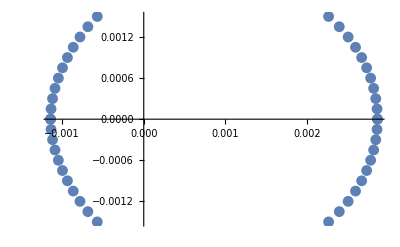

```mathematica
topShadow1=shadow1[[2]];
time1=shadow1[[1]]
bottomShadow1=Table[{topShadow1[[1,i,1]],-topShadow1[[1,i,2]]},{i,1,Length[topShadow1[[1]]]}];
completeShadow1=Join[topShadow1[[1]],bottomShadow1];
ListPlot[completeShadow1]
```

```mathematica
dϕ1=topShadow1[[1,Length[topShadow1[[1]]]-1,1]]
dϕ2=topShadow1[[1,Length[topShadow1[[1]]],1]]
const=5;
initial2=0;
While[initial2/(initial2+const)*dθmax2≤dθmax1,
initial2+=1;
]
max2=100;dθmax2=0.0023;
shadow2=AbsoluteTiming[findShadow[τValue,ics,initial2,max2,dθmax2,const,eps,1]];
```

-0.00046339

0.00205551

InterpolatingFunction::dmval: Input value {11.9499, 1.57131} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

553.45654

0.0020125

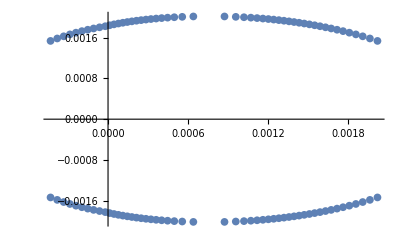

```mathematica
topShadow2=shadow2[[2]];
time2=shadow2[[1]]
bottomShadow2=Table[{topShadow2[[1,i,1]],-topShadow2[[1,i,2]]},{i,1,Length[topShadow2[[1]]]}];
completeShadow2=Join[topShadow2[[1]],bottomShadow2];
topShadow2[[1,Length[topShadow2[[1]]],2]]
ListPlot[completeShadow2]
```

12.748123

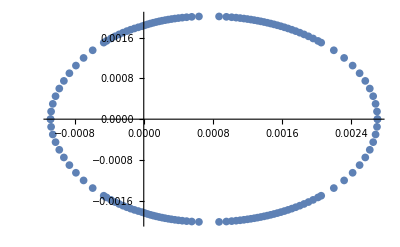

```mathematica
(time1+time2)/60
ListPlot[Join[completeShadow1,completeShadow2]]
```